Defining constants in Si units

```mathematica
c= 3×10^8 m/s;h= 6.62606957*10^-34 J*s;h1=4.135667516*10^-15 eV*s; kB=1.3806488*10^-23 J/K;
```

Plotting Bose-Einstein distribution, adding units to make unitless exponent

```mathematica
BE[T_,λ_]:=1/(ⅇ^((h*c)/(λ*kB*T))-1);
```

Plotting as a function of wavelength

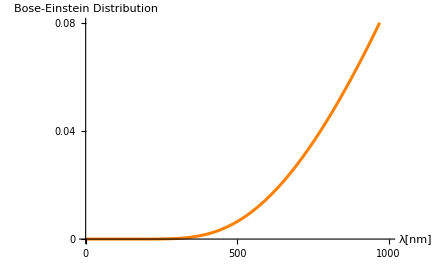

```mathematica
Plot[BE[5700*K,λ*10^-9 m],{λ,0,1000}, AxesLabel->{"λ[nm]","Bose-Einstein Distribution"},PlotRange->{{0,1000},{0,0.08}}, AspectRatio->1/GoldenRatio,PlotStyle->{{Orange,Thickness[0.005]}},Ticks->{{0,500,1000},{0,0.04,0.08}},AxesStyle->Directive[Gray,12]]
```

Plotting as a function of Temperature

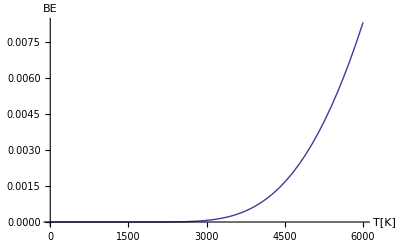

```mathematica
Plot[BE[T*K,500*10^-9 m],{T,0,6000}, AxesLabel->{"T[K]","BE"}]
```

Rayleigh-Jeans law

```mathematica
RJ[T_,λ_]:=(2c*kB*T)/λ^4((m^2*s)/(J*10^3)10^-9 m);
```

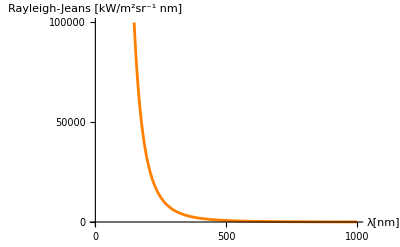

```mathematica
Plot[RJ[5778*K,λ*10^-9 m],{λ,0,1000},AxesLabel->{"λ[nm]","Rayleigh-Jeans [kW/m^2sr^-1 nm]"},PlotRange->{{0,1000},{0,100000}}, AspectRatio->1/GoldenRatio,PlotStyle->{{Orange,Thickness[0.005]}},Ticks->{{0,500,1000},{0,50000,100000}},AxesStyle->Directive[Gray,12]]
```

Plotting Planck's Law

```mathematica
PLaw[T_,λ_]:=(2h*c^2)/λ^5 1/(ⅇ^((h*c)/(λ*kB*T))-1)((m^2*s)/(J*10^3)10^-9 m);
```

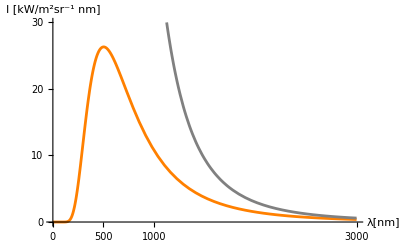

```mathematica
Plot[{PLaw[5778*K,λ*10^-9 m],RJ[5778*K,λ*10^-9 m]},{λ,0,3000}, AxesLabel->{"λ[nm]","I [kW/m^2sr^-1 nm]"},PlotRange->{{0,3000},{0,30}}, AspectRatio->1/GoldenRatio,PlotStyle->{{Orange,Thickness[0.005]},{Gray,Thickness[0.005]}},Ticks->{{0,500,1000,3000},{0,10,20,30}},AxesStyle->Directive[Gray,12]]
```

```mathematica
Frame->True,FrameTicks->{{{0,10,20,30},None},{{0,500,1000,3000},None}},FrameTicksStyle->Directive[Gray]
```